```mathematica
(* Небольшой пример для программы Mathematica.*)
```

```mathematica
(* Выражения в парных скобках со звёздочками --- комментарии. 
Выражения объединяются в блоки, отмеченные справа квадратной скобкой. *)
```

```mathematica
(* Для "выполнения" кода/инструкции блока нужно нажать Shift+Enter в любом месте блока. *)
```

```mathematica
(* То, чты мы пишем в интерактивном интерфейсе называется "блокнотом" (notebook, nb). *)
```

```mathematica
(* Синтаксис mathematica несколько непривычен для тех, кто работает с языками программирования. Это связано со спецификой решаемых в mathematica задач. *)
```

```mathematica
(* Переменные и присваивание.

Большая часть предопределённых переменных и функций начинаются с большой буквы, поэтому целесообразно использовать малые буквы.
*)
```

```mathematica
a=10;
b:=11
```

```mathematica
c=11.5
```

11.5

```mathematica
(* Здесь мы присвоили трём переменным три значения: два _целочисленных_ и одно вещественное.

В mathematica для указания, что число вещественное нужно задавать его с "точкой", иначе оно считается целым.

В этом примере можно увидеть несколько необычных способов задания переменных.

В самом простом случае, третья переменная c, при задании переменной и нажатии Shift+Enter, mathematica сразу же выполняет действие и по умолчанию показывает результат.

Если нам не нужно выводить результат или/и нужно ввести несколько переменных в одной строке, то можно разделить их "оператором" "точка-с-запятой", ; .

Переменной a присвоено значение, но оно не выведено на экран. 

Что касается переменной b, то это так называемое "отложенное" присваивание. Можно сказать, пользуясь аналогией с языками программирования, что переменная b введена, но пока она не использована, значение не присвоено.

Это полезно, когдо вычисление требует времени или даётся в виде, например, интеграла. *)
```

```mathematica
(* Рассмотрим простейший пример решения уравнения. *)
```

```mathematica
Solve[a x + b ==0,x]
```

{{x→-11/10}}

```mathematica
(* Ответ очевиден, но может удивить форма записи. Такая форма позволяет использовать результат позже в самой mathematica. *)
```

```mathematica
(* Матрицы и векторы. *)
```

```mathematica
tM={{1,1,0},{-1,0,1},{0,1,-1}}
```

{{1,1,0},{-1,0,1},{0,1,-1}}

```mathematica
(* Перед нами --- матрица, хотя форма записи и не обычна. Для привичной формы есть специальная "команда" *)
```

```mathematica
tM//MatrixForm
```

(1 | 1 | 0
-1 | 0 | 1
0 | 1 | -1)

```mathematica
(* Матрицу можно умножить на число, любое, при этом на это число умножаться все элементы матрицы. *)
```

```mathematica
(3-2 I) tM//MatrixForm
```

(3-2 ⅈ | 3-2 ⅈ | 0
-3+2 ⅈ | 0 | 3-2 ⅈ
0 | 3-2 ⅈ | -3+2 ⅈ)

```mathematica
(* Как видно из примера, не всегда нужно писать знак умножения, достаточно пробела, если всё однозначно. *)
```

```mathematica
(* Итак, чтобы задать матрицу, нужно перечислить её элементы в фигурных скобках. Аналогично для векторов. *)
```

```mathematica
tv={1,2,3}
```

{1,2,3}

```mathematica
tv//MatrixForm
```

(1
2
3)

```mathematica
(* Если умножить матрицу на вектор получится не совсем то, на что можно было бы рассчитывать: *)
```

```mathematica
tM tv//MatrixForm
```

(1 | 1 | 0
-2 | 0 | 2
0 | 3 | -3)

```mathematica
(* Казалось бы должен получиться вектор, а получилась матрица. Если присмотреться, то можно увидеть, как происходит это умножение. *)
```

```mathematica
(* Для получения ожидаемого результата надо использовать "специальное" умножение. *)
```

```mathematica
tM.tv//MatrixForm
```

(3
2
-1)

```mathematica
(* Адресация элементов. 

Выше мы видели ответ для решения линейного уравнения. Ответ очень похож на "матрицу".

Мы можем обратиться к элементам матриц и векторов.
*)
```

```mathematica
tM[[1,1]]
```

1

```mathematica
Out[11][[2]]
```

2

```mathematica
Out[4][[1]]
```

{x→-11/10}

```mathematica
(* В этих примерах показано как получить заданный элемент матрицы/массива/таблицы/списка.

Для этого нужно указать в ДВОЙНЫХ квадратных скобках номер, если это вектор или номер строки и номер столбца через запятую, если это матрица. 

Здесь же показано как можно обратиться к полученным ранее ответам: весь вывод в mathematica сопровождается префиксами Out[ЧИСЛО], что мы и использовали выше. *)
```

```mathematica
Out[7][[2]]
```

{-3+2 ⅈ,0,3-2 ⅈ}

```mathematica
(* Заметим, что если для матрицы указать не два числа, а одно, то мы получим вектор (строку) из матрицы, что, впрочем, ожидаемо. *)
```

```mathematica
(* Графики функций.

В mathematica можно строить графики функций, хотя подстройка формата вывода не столь проста. *)
```

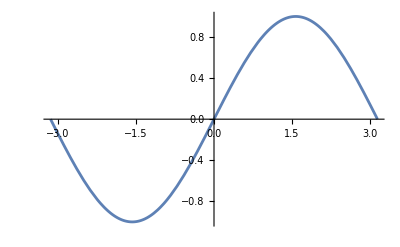

```mathematica
Plot[Sin[x],{x,-Pi,Pi}]
```

```mathematica
(* Возьмём более "хитрый" пример и построим несколько графиков сразу. *)
```

```mathematica
fF[a_]:=Sin[a x]
```

```mathematica
(* Здесь мы используем довольно таки "крутой" способ: мы заводим "функцию" fF с одним аргументом, которая на деле возвращает другую функцию. Такие выражения принято называть _анонимные_ функции или _лямбда_ функции. *)
```

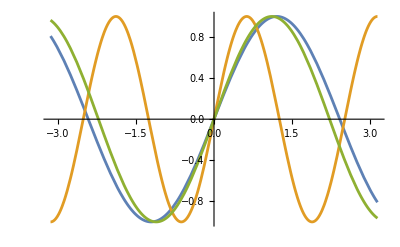

```mathematica
Plot[{fF[1.3],fF[2.5],fF[Sqrt[2]]},{x,-Pi,Pi}]
```

```mathematica
(* Обратим внимание, что здесь нам приходит "на выручку" именно "отложенное" присваивание. *)
```

```mathematica
(* Заметим, что функция Plot строит графики *только* функций. Если у нас есть таблицы с данными, для "постройки" графика есть отдельная функция ListPlot. *)
```